```mathematica
IntermediateFunction[x_,a_,b_,c_]:=a*x (1+b*Log[x])/(1+c*x)
```

## σ_T

```mathematica
σTsmall[β_]:=2 π β^2(1+β^2(-BesselK[1, β]^2+BesselK[0,β]BesselK[2,β]))
```

### Attractive

```mathematica
γ[β_]:=Sqrt[π/β] Erfi[Sqrt[ProductLog[2β]/2]]-1/ProductLog[2β]
```

```mathematica
σTlargeatt[β_]:=π((1+Log[β]-1/(2 Log[β]))^2-1/γ[β]^2)
```

```mathematica
βlow=1;
βhigh=50;
```

```mathematica
sol=FindRoot[{σTsmall[βlow]==IntermediateFunction[βlow,a,b,c],(D[σTsmall[β],β]/.β->βlow)==(D[IntermediateFunction[β,a,b,c],β]/.β->βlow),σTlargeatt[βhigh]==IntermediateFunction[βhigh,a,b,c]},{{a,5},{b,1},{c,1}}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{a→257.469,b→1.41956,c→30.0011}

```mathematica
σT[β_]:=Piecewise[{{σTsmall[β],β≤βlow},{IntermediateFunction[β,a,b,c]/.sol,β>βlow&&β<βhigh},{σTlargeatt[β],β≥βhigh}}]
```

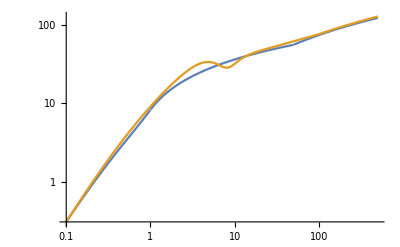

```mathematica
P1=LogLogPlot[{σT[β],s[β]},{β,0.1*βlow,10*βhigh}]
```

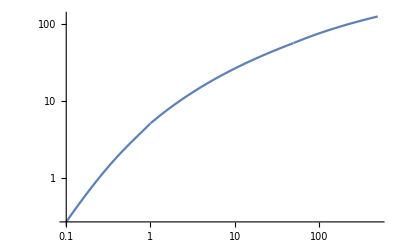
```mathematica
Show[-Graphics-,P1]
```

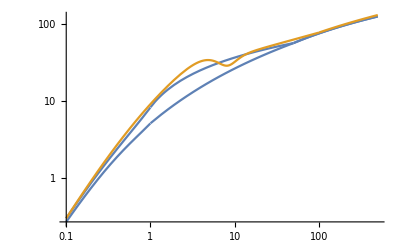

### Repulsive

```mathematica
σTlargerep[β_]:=π*1.20*ProductLog[2β]^2
```

```mathematica
βlow=0.5;
βhigh=10;
```

```mathematica
sol=FindRoot[{σTsmall[βlow]==IntermediateFunction[βlow,a,b,c],(D[σTsmall[β],β]/.β->βlow)==(D[IntermediateFunction[β,a,b,c],β]/.β->βlow),σTlargerep[βhigh]==IntermediateFunction[βhigh,a,b,c]},{{a,5},{b,1},{c,0.1}}]
```

{a→39.752,b→0.608472,c→5.1073}

```mathematica
σT[β_]:=Piecewise[{{σTsmall[β],β≤βlow},{IntermediateFunction[β,a,b,c]/.sol,β>βlow&&β<βhigh},{σTlargerep[β],β≥βhigh}}]
```

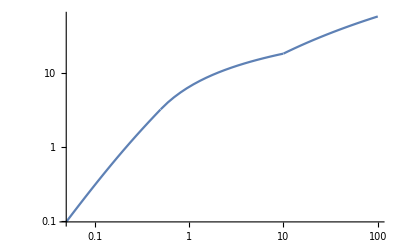

```mathematica
LogLogPlot[σT[β],{β,0.1*βlow,10*βhigh}]
```

## σ_V

```mathematica
σVsmall[β_]:=4 π β^2(1/2+4β^2(-BesselK[1,2 β]^2+BesselK[0,2β]BesselK[2,2β]))
```

### Attractive

```mathematica
σVlargeatt[β_]:=π/2(1+Log[β]-1/(2 Log[β]))^2
```

```mathematica
βlow=0.5;
βhigh=20;
```

```mathematica
sol=FindRoot[{σVsmall[βlow]==IntermediateFunction[βlow,a,b,c],(D[σVsmall[β],β]/.β->βlow)==(D[IntermediateFunction[β,a,b,c],β]/.β->βlow),σVlargeatt[βhigh]==IntermediateFunction[βhigh,a,b,c]},{{a,5},{b,1},{c,0.1}}]
```

{a→8.51843,b→0.288505,c→0.639636}

```mathematica
σV[β_]:=Piecewise[{{σVsmall[β],β≤βlow},{IntermediateFunction[β,a,b,c]/.sol,β>βlow&&β<βhigh},{σVlargeatt[β],β≥βhigh}}]
```

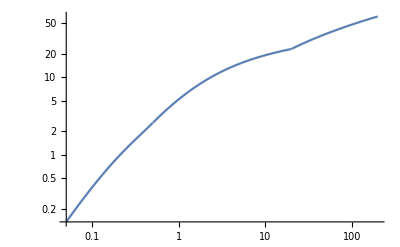

```mathematica
LogLogPlot[σV[β],{β,0.1*βlow,10*βhigh}]
```

### Repulsive

```mathematica
σVlargerep[β_]:=0.793 π ProductLog[2β]^2+π/2(ProductLog[4π β^2]^2/4-ProductLog[2β]^2)
```

```mathematica
βlow=0.5;
βhigh=5;
```

```mathematica
sol=FindRoot[{σVsmall[βlow]==IntermediateFunction[βlow,a,b,c],(D[σVsmall[β],β]/.β->βlow)==(D[IntermediateFunction[β,a,b,c],β]/.β->βlow),σVlargerep[βhigh]==IntermediateFunction[βhigh,a,b,c]},{{a,5},{b,1},{c,0.1}}]
```

{a→31.3355,b→0.537149,c→5.61824}

```mathematica
σV[β_]:=Piecewise[{{σVsmall[β],β≤βlow},{IntermediateFunction[β,a,b,c]/.sol,β>βlow&&β<βhigh},{σVlargerep[β],β≥βhigh}}]
```

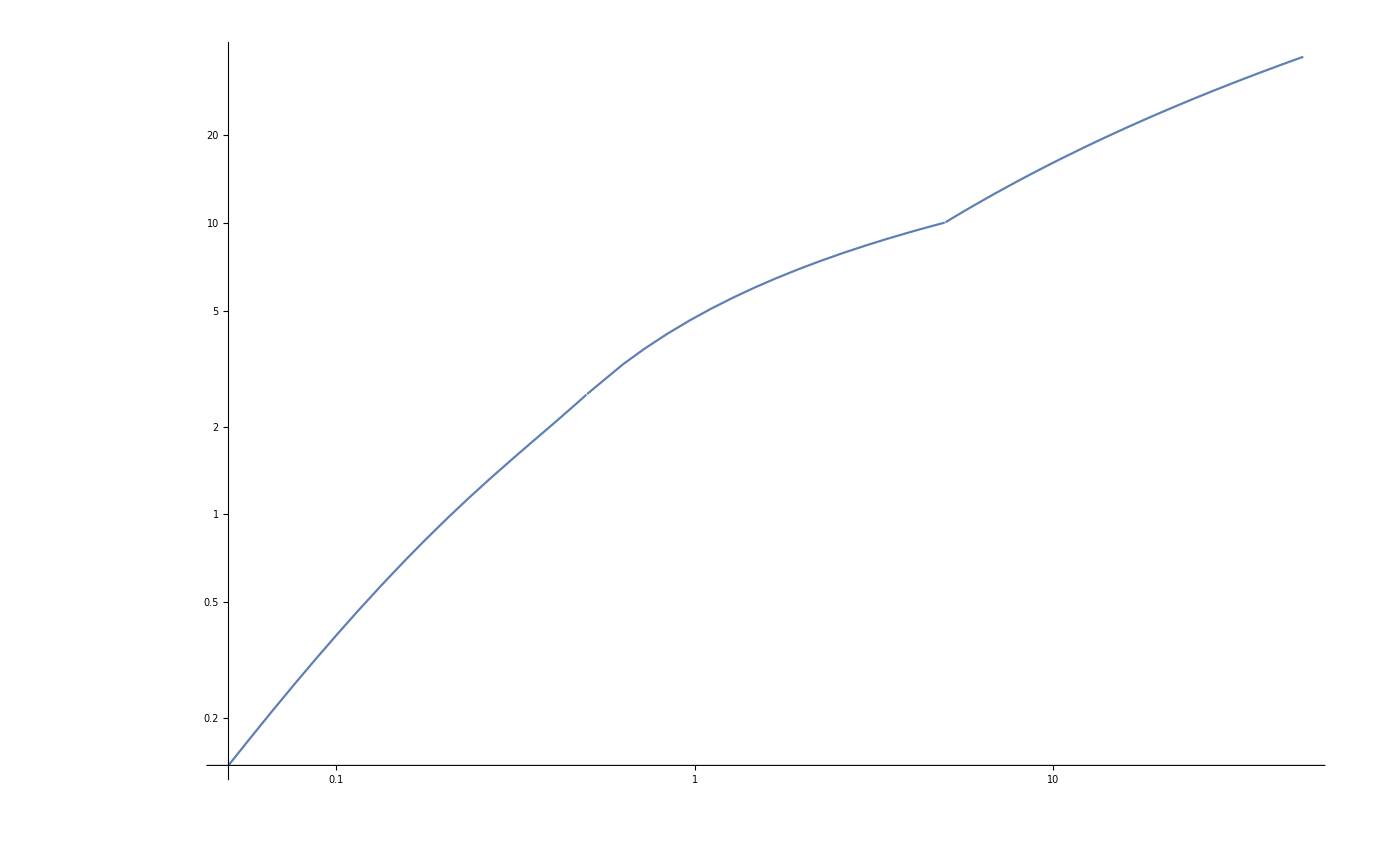

```mathematica
LogLogPlot[{σV[β]},{β,0.1*βlow,10*βhigh}]
```